# Beam Profiling Documentation

```mathematica
ClearAll["Global`*"]
```

ATTENTION: Every time you use open this notebook, evaluate the whole notebook first: Evaluation → Evaluate Notebook. If you do not do this, intra-document links will not work. Every time you run another notebook (especially those with ClearAll[“Global`*”], rerun this entire notebook.

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Notebook"],Background->GrayLevel[0.99]],Cell[StyleData["Input"],Background->LightYellow],Cell[StyleData["Output"],Background->LightGreen],Cell[StyleData["Text"],Background->LightBrown],Cell[StyleData["Chapter"],Background->GrayLevel[.9]]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

```mathematica
CellPrint@Cell["Table of Contents","Chapter"(*format style option*),CellTags->{"toc"}]
```

## Table of Contents

Click on any of the links below to jump to that section. At each section there will be a link: back to the table of contents, to beginning of the section before, and to the beginning of the section after.

```mathematica
Framed[Column[{Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}],
Hyperlink["Introduction",{EvaluationNotebook[],"intro"}],
Hyperlink["Links to Helpful Websites",{EvaluationNotebook[],"links"}],
Hyperlink["Introduction Part 2 (Properties of beams)",{EvaluationNotebook[],"intro2"}],
Hyperlink["Introduction Part 3 (Gaussian Beam Math)",{EvaluationNotebook[],"intro3"}],
Hyperlink["The Thorlabs Camera",{EvaluationNotebook[],"camera"}],
Hyperlink["The Need to Decimate",{EvaluationNotebook[],"deci"}],
Hyperlink["What is a Module?",{EvaluationNotebook[],"mod"}],
Hyperlink["Code Used to Decimate",{EvaluationNotebook[],"decicode"}],
Hyperlink["Fitting an Image",{EvaluationNotebook[],"fitim"}],
Hyperlink["Working with Multiple Images",{EvaluationNotebook[],"work1"}],Hyperlink["The End...?",{EvaluationNotebook[],"ending"}]

}],RoundingRadius->5]
```

Table of Contentsiqxbm_shmtocButtonData
Introductioniqxbm_shmintroButtonData
Links to Helpful Websitesiqxbm_shmlinksButtonData
Introduction Part 2 (Properties of beams)iqxbm_shmintro2ButtonData
Introduction Part 3 (Gaussian Beam Math)iqxbm_shmintro3ButtonData
The Thorlabs Cameraiqxbm_shmcameraButtonData
The Need to Decimateiqxbm_shmdeciButtonData
What is a Module?iqxbm_shmmodButtonData
Code Used to Decimateiqxbm_shmdecicodeButtonData
Fitting an Imageiqxbm_shmfitimButtonData
Working with Multiple Imagesiqxbm_shmwork1ButtonData
The End...?iqxbm_shmendingButtonData

```mathematica
CellPrint@Cell["Introduction","Chapter"(*format style option*),CellTags->{"intro"}]
```

## Introduction

```mathematica
Print["Before:",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["After: ",Hyperlink["Introduction Part 2",{EvaluationNotebook[],"intro2"}]]
```

Before:Table of Contentsiqxbm_shmtocButtonData

After: Introduction Part 2iqxbm_shmintro2ButtonData

Hi. It’s nice to meet you. Let’s get down to business. The contents of this notebook will help you learn what it takes to profile a laser beam. Put simply, profiling a beam means determining certain properties of the beam. I’ll tell you about these mysterious properties later on. For now I have some introductory things to talk to you about. 

If you are new to Mathematica read the following. If you are not new to Mathematica, STILL read the following:
I am not going to tell you about basic Mathematica syntax. That is beyond the scope of this notebook. However, I will be documenting each line of code, telling you what it does and sometimes how it does what it does. I bet you all my bitcoins (zero bitcoins) that there will be function/syntax that you have not seen. Don’t freak out when you gaze upon such bewildering code. Reread the code a few times, and if you still do not understand, look up the information online. 

A specific website that I find helpful is Mathematica Stack Exchange. It is a question and answers forum. Directly below in the green cells are links to questions and answers that I found helpful when creating this program. I am also listing links to some official Mathematica documentation pages. Now you must understand that official Mathematica documentation is generally not helpful (it either overloads you with too much or undercuts you with too little). (However, once in a while I find something on there that is helpful). Some of the following links are about (random) things I found interesting. I’m not going to bother organizing these links into those three categories, not because I’m lazy, but because I don’t remember that much about them. Come back to this list if you run into confusing code later on, or if you feel like going on an adventure. 

The first two links are to the homepages of Mathematica Stack Exchange and Wolfram Documentation, respectively. The third link is to a Mathematica Stack Exchange page hosting a bunch of links to different questions (and it is organized unlike my list) that might help you out a lot. The forth link is a collection of links to a google doc that I created (because I didn’t want to type 3 pages of urls in Mathematica). You can get a sense of what the urls are about in the google doc by looking at the text near the end of the url.

```mathematica
CellPrint@Cell["Links to Helpful Sites/Pages:","Text"(*format style option*),CellTags->{"links"}]
Framed[Column[{
Hyperlink["Mathematica Stack Exchange","https://mathematica.stackexchange.com"],
Hyperlink["Wolfram Language and System Documentation Center","http://reference.wolfram.com/language/"],
Hyperlink["Where can I find examples of good Mathematica programming practice?","https://mathematica.stackexchange.com/questions/18/where-can-i-find-examples-of-good-mathematica-programming-practice/"],
Hyperlink["All Other Links","https://docs.google.com/document/d/12XCEQh0dlDfbduIREJF1CPT0YKD78AzRL2Te7JkuUcw/edit?usp=sharing"]}],RoundingRadius->5]
```

Links to Helpful Sites/Pages:

[Mathematica Stack Exchange](https://mathematica.stackexchange.com)
[Wolfram Language and System Documentation Center](http://reference.wolfram.com/language/)
[Where can I find examples of good Mathematica programming practice?](https://mathematica.stackexchange.com/questions/18/where-can-i-find-examples-of-good-mathematica-programming-practice/)
[All Other Links](https://docs.google.com/document/d/12XCEQh0dlDfbduIREJF1CPT0YKD78AzRL2Te7JkuUcw/edit?usp=sharing)

```mathematica
Print["To Go Back to the TOC click this link:",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
```

To Go Back to the TOC click this link:Table of Contentsiqxbm_shmtocButtonData

As you have probably noticed by now, there is a color scheme to this notebook. In its current state: the notebook’s background is a very light gray, the title of each section is a dark gray, all text cells are a light brown, all input (what I refer to as the “code”) cells are light yellow, and all output cells are green. That is the way I set it up.

You also need to be aware of: File/folder paths. What is a file path you may ask? The green output below is a file path. In laymen’s terms, it is the path your computer takes to get to a file. (Path and Directory are interchangeable terms.) File paths are important for when you want to tell Mathematica where to look for something, which will be happening quite a bit in this document. Let’s see an example: 

To get the current Notebook Path/Directory, use the following code in yellow.

```mathematica
currentdirectory=NotebookDirectory[]
```

/Users/efm/Documents/Geneseo/Summer 2017/documentation/

Now let’s say that you want the path to a file on your computer, not this current notebook. 

If you are using a Mac you’re in luck (also good choice). You can easily copy the path of a file AND a folder. To do so: select the folder or file in Finder so that it is highlighted, and then press at the same time (simultaneously) these three buttons: option command c. This will copy the path. When pasting into Mathematica you need to enclose the path with quotes, effectively making it a string of characters.

If you are on a Windows computer, consider buying a Mac for your next laptop, because the only reliable way I know of for Windows is unintuitive. If you need the path of a only a file (not a folder) go to: Insert →File Path. To get the path of a folder, select a file in the folder and then manually delete the file name off the end of the path. 

Warning: File paths are written differently in macOS and Windows. (No one knows why Windows incorrectly represents file paths.) 

When importing files via a file path, the type of file (.jpeg, .pdf) needs to be at the end of the path. So make sure your computer displays file types at the end of file names. If it does not, look up how to do that. Because again, you need to include file type extensions at the end of file names in Mathematica.

There is one last thing I need to tell you. I created a package. A package is a group of functions that someone has coded to make it easier to do your job. These functions work like regular Mathematica function.  This package I created is called: FindingSpotSize. It is a folder containing files, each of which contains one function. Ignore what the name means for now. 

ATTENTION: The package does everything the rest of this documentation talks about, but allows you to do it in just a few lines of code. So we’re going to install it right now. To do this go to the folder that this documentation is in; that is to say go to the folder that has a path of:

```mathematica
NotebookDirectory[]
```

/Users/efm/Documents/Geneseo/Summer 2017/documentation/

Locate a folder called FindingSpotSize and copy it. Now you need to locate what is called your User Base Directory using the following line of code. If you evaluated the notebook in the beginning, the path should already be outputted.

```mathematica
$UserBaseDirectory
```

/Users/efm/Library/Mathematica

Locate this folder. There should be a folder inside of it called “Applications”. Enter this folder. Inside “Applications” is where you will paste my package. If done correctly on a Mac, the final path of my package in your Mathematica should look similar to: /Users/username/Library/Mathematica/Applications/FindingSpotSize. I’ll talk about using the package later on. 

But to make sure you installed it correctly, we are going to load the package into this Mathematica notebook, which will allow us to use its tools.

We are going to tell the notebook to go and get the package. << is shorthand for the Get command. You are going to see some warnings (4 probably, titled: Needs, Needs, Needs, General) but you can ignore those. 

If you see an error message: “Get: Cannot open FindingSpotSize”
Then you have not copied the FindingSpotSize folder correctly to the specified folder. Make sure to not rename the folder. 

Rerun the entire notebook once you have copied the folder into Applications.

```mathematica
<<FindingSpotSize`
```

Needs::nocont: Context FindingSpotSize`Coordify` was not created when Needs was evaluated.

Needs::nocont: Context FindingSpotSize`GaussianBeamFit` was not created when Needs was evaluated.

Needs::nocont: Context FindingSpotSize`AutoCroppingSuperRevised` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

Congrats! You made it through Introduction Part 1. You only have 90% of the documentation left! Move on to Introduction Part 2.

```mathematica
CellPrint@Cell["Introduction Part 2 (Properties of Beams)","Chapter"(*format style option*),CellTags->{"intro2"}]
```

## Introduction Part 2 (Properties of Beams)

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Introduction",{EvaluationNotebook[],"intro"}]]
Print["After: ",Hyperlink["Introduction Part 3",{EvaluationNotebook[],"intro3"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Introductioniqxbm_shmintroButtonData

After: Introduction Part 3iqxbm_shmintro3ButtonData

I mentioned profiling a laser beam earlier. Profiling a beam means determining certain properties about it. Once we know these properties we can do things with the beam. The properties that we are interested in are called: beam waist and the beam waist position. Dr. Marcus probably told you to read some optics textbook. I came onto the project knowing nothing about laser beams and I found the textbook to not be too helpful. It was pretty heavy with the math and did not have very clear explanations on what was happening. Once I eventually learned what was going on, I decided to write my own little description of laser beams. That is what you will now be reading. 

Here are some things you should know: First, we are making assumptions about the laser beam we are working with. We assume the laser beams are Gaussian laser beams. What the name means at the moment is not that important. What is important is that by assuming they are Gaussian, we are assuming that they are perfectly created laser beams. However, nothing is perfect, so there are differences in what we theorize and what we actually see. 

Second, whenever we talk about the cross sectional size of a beam, we are not talking about the distance from the center of the beam to its physical edges. Why is this? Its hard to define physical edges to a laser beam because the light doesn’t just stop at certain radius. If you shine a laser beam on a flat surface it might appear to you that at some radius away from what you perceive to be the center there is a distinct radius where the light stops existing. However, it doesn’t really stop existing beyond that radius, its just that you cannot see this faint light. So, it makes more sense to use some other measurement to determine the size of the beam. Thus, as is usually the case, people turned to math.

If I ask you for the size of the beam, I am asking you to tell me what the spot size of the beam is at that given location. (take away: size=spot size). The spot size is a measurement that is easily described and can be agreed upon by different scientists. 

Spot size is...

...the distance from the center of the beam...

...to where the intensity of the light...

...has dropped by one standard deviation. 

If the intensity of the light at the center of the beam has a value I_0, then the intensity of light one standard deviation away from this max value has an intensity of I_0/ⅇ^2, where ⅇ=2.718.
Third:

...the beam waist of a laser beam is...

...the smallest spot size the beam has. 

The beam waist is usually represented as w_0 or σ . The beam waist position usually represented as z_0 is where the beam waist is located. 

It is common to say that the axis the beam propagates along is the z axis, this explains why the beam waist position is represented as z_0. 

Forth, laser beam light wants to disperse. The more compact you make a laser beam, the more desperately it wants to disperse.

That is why it is observed that as beam waist decreases (that is to say you make the laser beam more compact with say a lens), the light diverges quicker.  

Fifth, I am by no means an expert on Gaussian laser beams. If you notice anything wrong in this documentation please correct it.

Below, I've attached the first page of a document I wrote. Click “view document” to view it and when you are done click “close document” to close it. You can view the full document in the folder that this notebook is in. The document is titled: testdoctry.pdf. Most of it is just restating what I said above but it also contains some graphics that might help you understand what is going on with Gaussian beam propagation. If I were you, I would only focus on the first page of the document as the last two pages are not important yet (and frankly I haven’t reviewed them). After you view the document move on to Introduction Part 3. You might have to side scroll inside this notebook to view the other pages of the document. 

If you have been reading this notebook non-stop from the beginning, right now would be a good time to take a break.

```mathematica
ButtonBar[{"View document":>Expression[doc=Import[currentdirectory<>"testdoctry.pdf"],{"Pages",1}],"close document":>Expression[Clear[doc]]}]
Dynamic[doc]
```

View document | close document

```mathematica
CellPrint@Cell["Introduction Part 3 (Gaussian beam Math)","Chapter"(*format style option*),CellTags->{"intro3"}]
```

## Introduction Part 3 (Gaussian beam Math)

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Introduction Part 2",{EvaluationNotebook[],"intro2"}]]
Print["After: ",Hyperlink["The Thorlabs Camera",{EvaluationNotebook[],"camera"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Introduction Part 2iqxbm_shmintro2ButtonData

After: The Thorlabs Cameraiqxbm_shmcameraButtonData

The time has come to learn the math used to described Gaussian laser beams. We will describe a laser beam through its intensity values at certain points in space. Using an equation with an x and y variable, you can describe how the intensity of a laser beam changes over a plane in space. 

ATTENTION: I got in the habit of thinking of the x variable as width and the y variable as height. You should do the same. To view a 3D plot representing intensity of a laser beam as a function of position in a plane click the “view plot” button. Close the plot when you’re done as that will make this notebook run faster.

```mathematica
ButtonBar[{"View plot":>Expression[plot=Plot3D[255 * ⅇ^((-(widthpos-80)^2)/30^2-(heightpos-64)^2/30^2)+0,{widthpos,1,160},{heightpos,1,128},PlotRange->All,MeshStyle->None,ColorFunction->GrayLevel,ViewAngle->.6,LabelStyle->Directive[Bold, Black,12],PlotRangePadding->None,PlotPoints->5,AxesLabel->{"width","height","Intensity"}],{"Pages",1}],"Close plot":>Expression[Clear[plot]]},Method->"Preemptive"]
Dynamic[plot]
```

View plot | Close plot

The equation we use to described the Intensity of a laser beam in a 2D plane is below. 

			Intensity(width position,height position)=maximumintensity * ⅇ^(^(^(^((-(widthposition-widthcenter)^2)/wwaist^2-(heightposition-heightcenter)^2/hwaist^2)))) +backgroundintensity 
The equation below allows for a non circular (potentially elliptical) laser beam by having separate width and height terms (major and minor axis terms). ⅇ=2.71828. The variables are in red. The constants in the equation are:  
											maximumintensity, 
widthcenter,
heightcenter,
wwaist,
hwaist, 
and 
backgroundintensity. 

Maximumintensity is the max intensity of the beam, which is located at the center. The widthcenter and heightcenter are the x and y coordinates of the beam’s center, respectively. wwaist and hwaist are the beam waists in a direction parallel to the width and height axes, respectively. Backgroudintensity is the intensity of background noise. 

Now we need to learn about the Thorlabs Camera.

```mathematica
CellPrint@Cell["The Thorlabs Camera","Chapter"(*format style option*),CellTags->{"camera"}]
```

## The Thorlabs Camera

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Introduction Part 3",{EvaluationNotebook[],"intro3"}]]
Print["After: ",Hyperlink["The Need to Decimate",{EvaluationNotebook[],"deci"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Introduction Part 3iqxbm_shmintro3ButtonData

After: The Need to Decimateiqxbm_shmdeciButtonData

I’ve told you about a lot of things so far, but I haven’t told you what we’re actually doing. Well here it goes (drum roll please): 

You will take pictures of the laser beam at different z (axis of propagation) position...

...and then use the tools I have provided in my package...

...to find the beam waist and beam waist’s position of the laser beam. 

After you know these two parameters you will be able to correctly manipulate the beam with lenses. We have a lot more to cover before you are ready to do that though. 

How do my tools determine the beam waist and beam waist position? They do what is called fitting the 3D intensity equation covered in the previous section to each of the images (or more specifically to the image data). 

But we are not going to focus on fitting just yet because we have to talk about the camera you will be using to take images. You will 

I’ve included the spec sheet for the camera below and you can access it via the buttons.  The only pieces of information you should care about are that: images taken with the camera have dimensions of 1280 pixels by 1024 pixels and that each pixel is square and has a side dimension of 5.2 micrometers (microns) (μm).

```mathematica
ButtonBar[{"View document":>Expression[doc2=Import[currentdirectory<>"cameraspecsfinal.pdf"],{"Pages",1}],"close document":>Expression[Clear[doc2]]}]
Dynamic[doc2]
```

View document | close document

In order to take pictures with the camera you will need to use the Thorlab Thorcam software. Here is some bad news. Thorcam software only runs on Windows, not macOS! If you have a Mac, you will need to either install a boot camp partition or use a virtual machine with usb device pass through. You’ll have to look up how to do both of those if you have a Mac. The link to the Thorcam software is below. With that sad news still fresh in your mind, continue on to next section.

```mathematica
Hyperlink["Thorcam Software","https://www.thorlabs.com/software_pages/ViewSoftwarePage.cfm?Code=ThorCam"]
```

[Thorcam Software](https://www.thorlabs.com/software_pages/ViewSoftwarePage.cfm?Code=ThorCam)

I intended to tell you how to use the Thorlabs software in this brown text box but I ran out of time. Maybe one day (probably never) I’ll fill in this section, but for now, it’ll be up to you to figure that out. I am attempting to tell you how to do everything else so please be understanding.

```mathematica
CellPrint@Cell["The Need to Decimate","Chapter"(*format style option*),CellTags->{"deci"}]
```

## The Need to Decimate

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["The Thorlabs Camera",{EvaluationNotebook[],"camera"}]]
Print["After: ",Hyperlink["Code Used to Decimate",{EvaluationNotebook[],"decicode"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:The Thorlabs Cameraiqxbm_shmcameraButtonData

After: Code Used to Decimateiqxbm_shmdecicodeButtonData

Image files taken with the Thorlab camera contain way more data than we need. The average picture from it contains about 1.3 million pixels. We only want tens of thousands of pixels so that our computations don’t take forever to run. Just think of it like this:  Two million dollars is a lot more than 10 thousand dollars...a lot more.

So how do we get from 1.3 million pixels to tens of thousands of pixels. We do something called decimation. When you decimate an image, you pick out the key pieces of information and throw out all the rest. 

When we are decimating an image we need to choose by how much we decimate it by. You have to ask yourself, do I want to turn that 1.3 million pixels into 100,000 pixels, 10,000 pixels or 1,000 pixels? YOu generally want as many as your computer can reasonable handle. 

Two different ways to decimate an image are demonstrated in this documentation (and these same two ways are used by my tools). The two ways are: automatic cropping and downsampling.

Automatic cropping, automatically crops the image to contain just the laser beam and just a little bit of the background. 

Downsampling is a little more difficult to explain and better seen in an example. So here’s the example of downsampling:

If you have not taken a linear algebra course: a matrix is a grid of numbers. Representing data in such a grid allows for some very cool math.

Consider the matrix of values below. This matrix of values could represent pixel intensity values from an image sensor. That’s right folks, that camera on your phone contains an image sensor. And on this image sensor is a grid of pixels. And each pixel records a value (or a set of values). 

Each number represents a value of the intensity of light that hit that pixel. 

In just this example, 0 means the pixel registered light hitting it (so this pixel will be white), and 1 means the pixel did not register light (so this pixel will be black). This is an 8 by 8 matrix.

```mathematica
examplearray=({{1, 1, 0, 0, 1, 1, 0, 0}, {1, 1, 0, 0, 1, 1, 0, 0}, {0, 0, 1, 1, 0, 0, 1, 1}, {0, 0, 1, 1, 0, 0, 1, 1}, {1, 1, 0, 0, 1, 1, 0, 0}, {1, 1, 0, 0, 1, 1, 0, 0}, {0, 0, 1, 1, 0, 0, 1, 1}, {0, 0, 1, 1, 0, 0, 1, 1}});
```

An image produced by this matrix of values would look like the grid of pixels below. The tick marks are aligned with the center point of each pixel. I’ve included red grid lines that represent the edges of pixels so that you can make out each pixel.

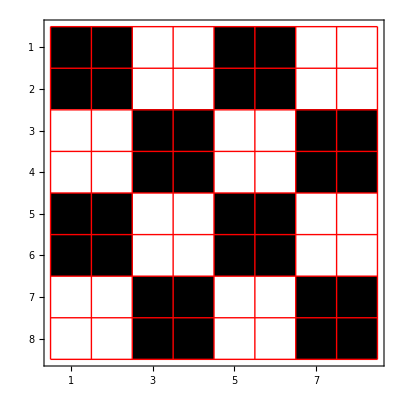

```mathematica
ArrayPlot[examplearray,Frame->True,Mesh->True,FrameTicks->All,MeshStyle->Red]
```

If I now Downsample the data to get a matrix whose both height and width dimensions has been divided by 2, I get this matrix:

```mathematica
resampledexamplearray=ArrayResample[examplearray,{4,4},Resampling->"Nearest"];
```

```mathematica
resampledexamplearray//MatrixForm
```

(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1)

Made into an image, the downsampled matrix looks like the following:

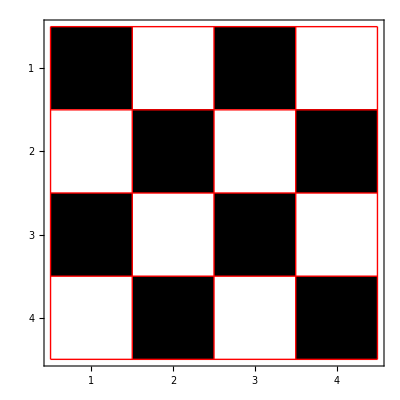

```mathematica
ArrayPlot[resampledexamplearray,Frame->True,Mesh->True,FrameTicks->All,MeshStyle->Red]
```

You’ll notice that the matrix is now 4 by 4 pixels. This is because of the way I asked Mathematica to Downsample the image. Mathematica starting at the top left of the matrix, looked at every 2 by 2 block of pixels. It found the average value in each 2 by 2 block and then replaced the 2 by 2 block with 1 pixel with the average value. Not all images look exactly the same when downsampled. It just so happens that this was the case due to my equisite planning.

Ideally, when decimating an image of the beam, you want to crop the most and downsample the least, as cropping throws out useless image data (the black background) and keeps the important image data (the beam) untouched, whereas downsampling introduces new intensity values everywhere in the image because it is averaging, therefore affecting the data. It was with this philosophy in mind that I created my decimation tool.

To recap: 

1)Decimation is done to save computing time. 
2)There are two methods to doing decimation that I cover and use: 
	a) automatic cropping
	b) downsampling
3) Automatic cropping is preferred as it  leaves the image data we care about untouched.
4) We can choose how much we want to decimate an image by. We can choose how much to crop it by. We can choose how much to Downsample it by.

Automatic cropping at first appeared to be a perfect solution, however, perfection does not exist. It was decided by Dr. Marcus and the group, that an image should not take more than 2 minutes to be analyzed by the computer (the range of potential times ranged from 10 secs to 10 minutes). It was found that automatic cropping does not save time with large beams. Here’s why:

For explanation purposes lets say the amount of pixels in a image that demands exactly 2 minutes of computing time when analyzed is represented by the variable p. If a beam is sufficiently large, the automatic cropping tool will output an image with an amount of pixels ≥ p. Thus, on these sufficiently large beams, the auto-cropping program produces images that will take more than 2 minutes of analysis. Further, it was found that downsampling an image from 1.3 million pixels to a p number of pixels did not significantly affect the data. 

Therefore:
Auto-cropping is used on images of beams that will result in a final image with an amount of pixels less than p. (that is to say auto-cropping is used on beams smaller than a certain size). 
Downsampling is used on images of beams that would have resulted in an amount of pixels greater than p had these same images been auto-cropped. When downsampled, images are always downsampled to have an amount of pixels equal to p.

With any of the analysis that we do on an image, we will have to convert it to real world units. For example, we have to go from pixels to millimeters. With automatic cropping this pixel to meter conversion is easy, as one pixel has a side dimensions always equal to 5.2 μm. However,  downsampling, always changes a pixel’s side dimension to 10.4 μm. This is from one pixel being replaced by a 2 by 2 block of pixels. The dimensions that I chose to have an image downsampled to were specifically chosen to maintain the original dimension ratio.

```mathematica
CellPrint@Cell["What is a Module?","Chapter"(*format style option*),CellTags->{"mod"}]
```

## What is a Module?

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["The Need to Decimate",{EvaluationNotebook[],"deci"}]]
Print["After: ",Hyperlink["Code Use to Decimate",{EvaluationNotebook[],"decicode"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:The Need to Decimateiqxbm_shmdeciButtonData

After: Code Use to Decimateiqxbm_shmdecicodeButtonData

You can skip this section if you do not plan on fixing or changing the package code. If you do plan on editing the package code, you will have to edit the .m files found in the “FindingSpotSize” folder. You will also have to be familiar with the Module Function and the format for .m files.

We are going to take a short break from talking about decimation and talk about a function in Mathematica I used a lot when creating my tools. The function is Module. You will need to understand what a module is, if you ever want to change, or add to, my FindingSpotSize package.

You can always ask Mathematica to tell you about a function by putting a question mark in front of the Function. However as you see below, this information is not always helpful.

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

So don’t count on Mathematica to help you use its functions.

A module establishes a local namespace or scope for variables. Module allows you to use already defined variables as if they were not already defined.

Let us see an example. 
First, I am going to assign a value of 7 to a variable x for no particular reason.

```mathematica
x=7
```

7

Now I am going to create a module. Don’t worry about the code I use to do it yet, just focus on the output for now. Inside the module I am going to create the variable x. I am then going to assign a value of 3 to x. The output should be 3 and it is. 

This is a nice feature of a module. Anything that goes into a module assumes a new identify as long as it is in the module and when you are outside of the module everything goes back to the way it was.

```mathematica
Module[{x},x=3;Print["The value of x inside the module: "<>ToString[x]]]
```

The value of x inside the module: 3

Now I am going to ask Mathematica to tell me what the value of x is outside of the module. If I setup the module correctly, the value outputted should be 7, and it is.

```mathematica
x
```

7

You can even do calculations in a module. I am going to assign x a value of 5 and then add 6 to this value. It should be noted that module outputs the result of the last entry inside it. In this case it outputs the result of  x+6

```mathematica
Module[{x},x=5;x+6]
```

11

The format of Module is as follow:

Module[{list of variables you want to use in your module},each line of code; separated; by semicolons; with the last entry being the returned output]

A multivariable and multiple calculation Module looks like the below line of code. You will see that the last entry is a list. What I like about Module is that you can return a list as an output.

```mathematica
Module[{x,y,z},x=8;y=2;z=x+y;{x,y,z}]
```

{8,2,10}

I mentioned before that anything that goes into a Module assumes a new identity. That is only true if you make sure to list the variable in the section of Module I called: list of variables you want to use in your module.

x still has a value of 7 in the global scope (outside of the module) . If I do not list x as a variable in the list of variables you want to use in your module list, then the module does not give x a temporarily new identity. That can be seen below where I do not list it.

```mathematica
Module[{y,z},y=2;z=x+y;{x,y,z}]
```

{7,2,9}

It is important to know that if do not list x intially but do assign it a value inside the module, I change its value outside of the module (because, well, it never really was officially in the module). That can be seen below where I assign x a value of 6 inside the module and then ask for Mathematica to tell me what it thinks the value of x is. Instead of returning 7, Mathematica will tell us x now has a value of 6.

```mathematica
Module[{y,z},x=6;y=2;z=x+y;{x,y,z}]
```

{6,2,8}

```mathematica
x
```

6

Also,

```mathematica
Module[{x},x=3]
```

3

is equivalent to:

```mathematica
Module[{x=3},x]
```

3

You can assign initial values to the variables inside the list of variables you want to use in your module.

Module is a very powerful when used correctly because it can allow for actually programs to be written in Mathematica. You might be asking where exactly does one use Module. Well you use it in user defined functions. I am going to write out the code to a random user defined function using Module below and then I will explain it.

```mathematica
add2[number_]:=Module[{num=number,newnum},newnum=num+2;{num,newnum}]
```

```mathematica
add2[5]
```

{5,7}

So this function will add 2 to any number entered into it. Let’s break this code down into pieces. First, I write the function’s name and decide what to call the input value.

add2[number_]

For any function you create, you put an underscore after the name of the variable you use for an input value.

Then I add

:=

to get

add2[number_] :=

When you create a function you use you use “:=”.

```mathematica
f[t_]:=t^2
```

```mathematica
f[5]
```

25

I then create the module. Notice there is a comma between the list of variables and the area where computations happen.

add2[number_] :=Module[{},]

And then I tell it what variables I will be using inside the module. I will be using a variable called “num” and “newnum”. This part of the process always requires foresight.

add2[number_] :=Module[{num, newnum},]

I then make it so that “num” has an initial value equal to the input value “number”. This part of the process creates the bridge that spans from the outside of the module to inside the module.

add2[number_] := Module[{num = number, newnum},]

Before I thought of what variables I needed inside the module, I thought about how I was going to return the output. I decided that I would assign the result of the decision to the a variable called “newnum”. Hence, why I created a “newnum” variable inside the module earlier and said that it required foresight. 

So now I perform adding 2 to num, and assign the result to variable “newnum”. Notice that I use “num” instead of number in the addition. It is best to use the variables local to the Module when doing anything inside the module.

add2[number_] := Module[{num = number, newnum}, newnum = num + 2]

I then decide what the output will be. I decided it will be a list where the first element is the inputted value, and the second element is the value of the result of the addition.

add2[number_] := Module[{num = number, newnum},newnum = num + 2;{num,newnum}]

And that is it. I hope you have a better understanding of what a module is. If you still don’t understand, ask the internet for help. I’m sure there are better explanations online. No matter what you do, make sure you understand Module and how to use it to create a user defined (“do something”) function (not a math function) before moving on.

ATTENTION: After coming back to this program after a few months of doing other things, I now realize I probably could have done everything not using module. But since that is what I used and since I am not going to change it all to not use module, I think it was still worth your while to read about Module.

```mathematica
CellPrint@Cell["Code Used to Decimate","Chapter"(*format style option*),CellTags->{"decicode"}]
```

## Code Used to Decimate

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["What is a Module?",{EvaluationNotebook[],"mod"}]]
Print["After: ",Hyperlink["Fitting an Image",{EvaluationNotebook[],"fitim"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:What is a Module?iqxbm_shmmodButtonData

After: Fitting an Imageiqxbm_shmfitimButtonData

My decimation process is performed by the tool TotallyDecimate. Below is a flowchart of the process that occurs in TotallyDecimate. I’ll walk you through the process. At this point, you are not expected to know about the elements in the flowchart. In fact don’t look at the flow chart for more than 5 seconds until you’ve finished reading this section. For now, just know that the tool follows a process.

```mathematica
?TotallyDecimate
```

TotallyDecimate[imdata] will do the most effecient and effective decimation possible and will return {data,pixel multiplier to mm value}

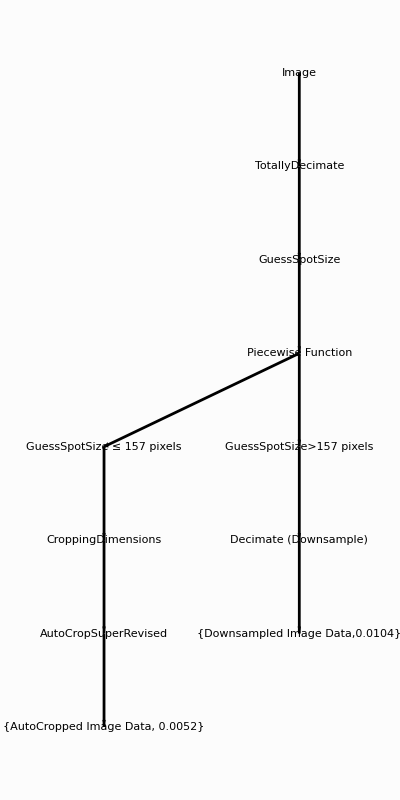

```mathematica
LayeredGraphPlot[{"Image"->"TotallyDecimate","TotallyDecimate"->"GuessSpotSize","CroppingDimensions"->"AutoCropSuperRevised","GuessSpotSize"->"Piecewise Function","Piecewise Function"->"GuessSpotSize ≤ 157 pixels","Piecewise Function"-> "GuessSpotSize>157 pixels","GuessSpotSize>157 pixels"->"Decimate (Downsample)","Decimate (Downsample)"->"{Downsampled Image Data,0.0104}","GuessSpotSize ≤ 157 pixels"->"CroppingDimensions","AutoCropSuperRevised"-> "{AutoCropped Image Data, 0.0052}"},Top,VertexLabeling->True,PlotStyle->{Black,Arrowheads[{{0.07,0.6}}],Thickness[0.005]}(*, ImageSize->{700,350}*),PlotRangePadding->None,DirectedEdges->True,AspectRatio->2,ImagePadding->Automatic,Background->GrayLevel[.99]]
```

## Image

The first thing that happens in the decimation process is that the image gets imported into Mathematica. The image taken with the Thorlab camera is a bitmap image (it could be different but as I mentioned before we only take images in the bitmap format). This file type is chosen because it does not compress the image data at all. 

The first thing to do when importing an image is to give Mathematica the file path to the image. For the purposes of this explanation, I will be importing an image located in the documentation folder. It is an image of a laser beam. We will be using the Import function.

```mathematica
?Import
```

Import[file] imports data from a file, returning a complete Wolfram Language version of it.
Import[file,elements] imports the specified elements from a file.
Import["http://url",…] and Import[ftp://url,…] import from any accessible URL.

To import an image we could just use the basic option:

Import["image path"]

But this imports the image as an image. You might be thinking, that sounds good, but, in fact, we do not want an image. We want just the data of the image, not the visual representation of the data that is commonly referred to as the image. To get just the data of the image we specify Data:

Import["image path", "Data"]

Let us look at the differences in importing the image and importing the image data:

First, I am importing the image:

```mathematica
Import[currentdirectory<>"image.bmp"]
```

-Graphics-

Second, I am importing the image data. Below is the data that is used to form the visual image above.

```mathematica
Import[currentdirectory<>"image.bmp","Data"]
```

{1}
 |  |  |  |

They look a bit different, right? If on the output of the second one you just see {... 1 ...}, click “show more” at the bottom of the white box and you will be shown a list of lists of values (mostly zeros).

### Side Note on Using <>:

You might be wondering about the path I specified in the Import function because it doesn’t look like a path I’ve shown you before:

currentdirectory <> "image.bmp"

Earlier, the directory of the documentation folder which houses the image, was saved to the variable “currentdirectory” with the command:

currentdirectory = NotebookDirectory[]

The Notebookdirectory[] gives us a path that is very close to the path of the image that I want to import. However, it is missing the last piece of information, which is the image name and the image file type. I add this information to the path of the current folder’s directory using the less than and greater than signs in the configuration as seen below:

<>

And because a path is just a string of characters, I need the name of the file and image file type to be a string as well. I make it a string by enclosing it in quotes as such:

"image.bmp"

Also, <> is shorthand for the StringJoin function. That is to say:

```mathematica
"firstpart"<>"secondpart"<>"thirdpart"<>"etc"
```

firstpartsecondpartthirdpartetc

is equivalent to:

```mathematica
StringJoin["firstpart","secondpart","thirdpart","etc"]
```

firstpartsecondpartthirdpartetc

If I put it all together I get a string referring to the path of the image. currentdirectory is a variable already assigned a string of characters representing the path of the image’s folder so no quotes are needed around it.

```mathematica
currentdirectory<>"image.bmp"
```

/Users/efm/Documents/Geneseo/Summer 2017/documentation/image.bmp

### End of Side Note on <>. Back to the Image Import :

The list of list of values from the raw data import is actually a matrix of values. A digital image can be represented as a matrix of values. Each element in such a matrix represents a pixel (picture element) of an image. In a colored image, each pixel contains three values. Each value represents an intensity value recorded in a different color space. The three different color spaces are Red, Green, and Blue. This is commonly referred to as RGB. Intensity values for any color space go from 0 to 255 inclusively (meaning 0 and 255 are acceptable color values). 

If you want to see what a pixel looks like, open up an image on your computer and keep zooming in until you cannot zoom in anymore. At this zoom level you should be able to see colored squares. Each of these squares is a pixel. 

Here’s the thing: the Thorlabs camera is a grayscale camera. It is not an RGB camera. Instead of recording intensity values for the three R, G, and B color spaces, the Thorlabs camera records intensity values only in the grayscale (or gray) color space. This means each pixel in an image taken with the Thorlabs camera only contains one value. 

Below is a grid. The top row is the grayscale intensity value and the bottom row is the color associated with that value. You can scroll to the right to view more of the colors.

```mathematica
arraydatalist=Array[(#&),256,{0,1}];
```

```mathematica
numbers=Array[{#//Round}&,256,{0,255.}];
```

```mathematica
colorchart={(GrayLevel[#])}&/@arraydatalist;
```

```mathematica
Grid[Join[numbers//Transpose,colorchart//Transpose,1],Frame->All,Background->White,ItemSize->{2, 2}]
```

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255
GrayLevel[0] | GrayLevel[Rational[1, 255]] | GrayLevel[Rational[2, 255]] | GrayLevel[Rational[1, 85]] | GrayLevel[Rational[4, 255]] | GrayLevel[Rational[1, 51]] | GrayLevel[Rational[2, 85]] | GrayLevel[Rational[7, 255]] | GrayLevel[Rational[8, 255]] | GrayLevel[Rational[3, 85]] | GrayLevel[Rational[2, 51]] | GrayLevel[Rational[11, 255]] | GrayLevel[Rational[4, 85]] | GrayLevel[Rational[13, 255]] | GrayLevel[Rational[14, 255]] | GrayLevel[Rational[1, 17]] | GrayLevel[Rational[16, 255]] | GrayLevel[Rational[1, 15]] | GrayLevel[Rational[6, 85]] | GrayLevel[Rational[19, 255]] | GrayLevel[Rational[4, 51]] | GrayLevel[Rational[7, 85]] | GrayLevel[Rational[22, 255]] | GrayLevel[Rational[23, 255]] | GrayLevel[Rational[8, 85]] | GrayLevel[Rational[5, 51]] | GrayLevel[Rational[26, 255]] | GrayLevel[Rational[9, 85]] | GrayLevel[Rational[28, 255]] | GrayLevel[Rational[29, 255]] | GrayLevel[Rational[2, 17]] | GrayLevel[Rational[31, 255]] | GrayLevel[Rational[32, 255]] | GrayLevel[Rational[11, 85]] | GrayLevel[Rational[2, 15]] | GrayLevel[Rational[7, 51]] | GrayLevel[Rational[12, 85]] | GrayLevel[Rational[37, 255]] | GrayLevel[Rational[38, 255]] | GrayLevel[Rational[13, 85]] | GrayLevel[Rational[8, 51]] | GrayLevel[Rational[41, 255]] | GrayLevel[Rational[14, 85]] | GrayLevel[Rational[43, 255]] | GrayLevel[Rational[44, 255]] | GrayLevel[Rational[3, 17]] | GrayLevel[Rational[46, 255]] | GrayLevel[Rational[47, 255]] | GrayLevel[Rational[16, 85]] | GrayLevel[Rational[49, 255]] | GrayLevel[Rational[10, 51]] | GrayLevel[Rational[1, 5]] | GrayLevel[Rational[52, 255]] | GrayLevel[Rational[53, 255]] | GrayLevel[Rational[18, 85]] | GrayLevel[Rational[11, 51]] | GrayLevel[Rational[56, 255]] | GrayLevel[Rational[19, 85]] | GrayLevel[Rational[58, 255]] | GrayLevel[Rational[59, 255]] | GrayLevel[Rational[4, 17]] | GrayLevel[Rational[61, 255]] | GrayLevel[Rational[62, 255]] | GrayLevel[Rational[21, 85]] | GrayLevel[Rational[64, 255]] | GrayLevel[Rational[13, 51]] | GrayLevel[Rational[22, 85]] | GrayLevel[Rational[67, 255]] | GrayLevel[Rational[4, 15]] | GrayLevel[Rational[23, 85]] | GrayLevel[Rational[14, 51]] | GrayLevel[Rational[71, 255]] | GrayLevel[Rational[24, 85]] | GrayLevel[Rational[73, 255]] | GrayLevel[Rational[74, 255]] | GrayLevel[Rational[5, 17]] | GrayLevel[Rational[76, 255]] | GrayLevel[Rational[77, 255]] | GrayLevel[Rational[26, 85]] | GrayLevel[Rational[79, 255]] | GrayLevel[Rational[16, 51]] | GrayLevel[Rational[27, 85]] | GrayLevel[Rational[82, 255]] | GrayLevel[Rational[83, 255]] | GrayLevel[Rational[28, 85]] | GrayLevel[Rational[1, 3]] | GrayLevel[Rational[86, 255]] | GrayLevel[Rational[29, 85]] | GrayLevel[Rational[88, 255]] | GrayLevel[Rational[89, 255]] | GrayLevel[Rational[6, 17]] | GrayLevel[Rational[91, 255]] | GrayLevel[Rational[92, 255]] | GrayLevel[Rational[31, 85]] | GrayLevel[Rational[94, 255]] | GrayLevel[Rational[19, 51]] | GrayLevel[Rational[32, 85]] | GrayLevel[Rational[97, 255]] | GrayLevel[Rational[98, 255]] | GrayLevel[Rational[33, 85]] | GrayLevel[Rational[20, 51]] | GrayLevel[Rational[101, 255]] | GrayLevel[Rational[2, 5]] | GrayLevel[Rational[103, 255]] | GrayLevel[Rational[104, 255]] | GrayLevel[Rational[7, 17]] | GrayLevel[Rational[106, 255]] | GrayLevel[Rational[107, 255]] | GrayLevel[Rational[36, 85]] | GrayLevel[Rational[109, 255]] | GrayLevel[Rational[22, 51]] | GrayLevel[Rational[37, 85]] | GrayLevel[Rational[112, 255]] | GrayLevel[Rational[113, 255]] | GrayLevel[Rational[38, 85]] | GrayLevel[Rational[23, 51]] | GrayLevel[Rational[116, 255]] | GrayLevel[Rational[39, 85]] | GrayLevel[Rational[118, 255]] | GrayLevel[Rational[7, 15]] | GrayLevel[Rational[8, 17]] | GrayLevel[Rational[121, 255]] | GrayLevel[Rational[122, 255]] | GrayLevel[Rational[41, 85]] | GrayLevel[Rational[124, 255]] | GrayLevel[Rational[25, 51]] | GrayLevel[Rational[42, 85]] | GrayLevel[Rational[127, 255]] | GrayLevel[Rational[128, 255]] | GrayLevel[Rational[43, 85]] | GrayLevel[Rational[26, 51]] | GrayLevel[Rational[131, 255]] | GrayLevel[Rational[44, 85]] | GrayLevel[Rational[133, 255]] | GrayLevel[Rational[134, 255]] | GrayLevel[Rational[9, 17]] | GrayLevel[Rational[8, 15]] | GrayLevel[Rational[137, 255]] | GrayLevel[Rational[46, 85]] | GrayLevel[Rational[139, 255]] | GrayLevel[Rational[28, 51]] | GrayLevel[Rational[47, 85]] | GrayLevel[Rational[142, 255]] | GrayLevel[Rational[143, 255]] | GrayLevel[Rational[48, 85]] | GrayLevel[Rational[29, 51]] | GrayLevel[Rational[146, 255]] | GrayLevel[Rational[49, 85]] | GrayLevel[Rational[148, 255]] | GrayLevel[Rational[149, 255]] | GrayLevel[Rational[10, 17]] | GrayLevel[Rational[151, 255]] | GrayLevel[Rational[152, 255]] | GrayLevel[Rational[3, 5]] | GrayLevel[Rational[154, 255]] | GrayLevel[Rational[31, 51]] | GrayLevel[Rational[52, 85]] | GrayLevel[Rational[157, 255]] | GrayLevel[Rational[158, 255]] | GrayLevel[Rational[53, 85]] | GrayLevel[Rational[32, 51]] | GrayLevel[Rational[161, 255]] | GrayLevel[Rational[54, 85]] | GrayLevel[Rational[163, 255]] | GrayLevel[Rational[164, 255]] | GrayLevel[Rational[11, 17]] | GrayLevel[Rational[166, 255]] | GrayLevel[Rational[167, 255]] | GrayLevel[Rational[56, 85]] | GrayLevel[Rational[169, 255]] | GrayLevel[Rational[2, 3]] | GrayLevel[Rational[57, 85]] | GrayLevel[Rational[172, 255]] | GrayLevel[Rational[173, 255]] | GrayLevel[Rational[58, 85]] | GrayLevel[Rational[35, 51]] | GrayLevel[Rational[176, 255]] | GrayLevel[Rational[59, 85]] | GrayLevel[Rational[178, 255]] | GrayLevel[Rational[179, 255]] | GrayLevel[Rational[12, 17]] | GrayLevel[Rational[181, 255]] | GrayLevel[Rational[182, 255]] | GrayLevel[Rational[61, 85]] | GrayLevel[Rational[184, 255]] | GrayLevel[Rational[37, 51]] | GrayLevel[Rational[62, 85]] | GrayLevel[Rational[11, 15]] | GrayLevel[Rational[188, 255]] | GrayLevel[Rational[63, 85]] | GrayLevel[Rational[38, 51]] | GrayLevel[Rational[191, 255]] | GrayLevel[Rational[64, 85]] | GrayLevel[Rational[193, 255]] | GrayLevel[Rational[194, 255]] | GrayLevel[Rational[13, 17]] | GrayLevel[Rational[196, 255]] | GrayLevel[Rational[197, 255]] | GrayLevel[Rational[66, 85]] | GrayLevel[Rational[199, 255]] | GrayLevel[Rational[40, 51]] | GrayLevel[Rational[67, 85]] | GrayLevel[Rational[202, 255]] | GrayLevel[Rational[203, 255]] | GrayLevel[Rational[4, 5]] | GrayLevel[Rational[41, 51]] | GrayLevel[Rational[206, 255]] | GrayLevel[Rational[69, 85]] | GrayLevel[Rational[208, 255]] | GrayLevel[Rational[209, 255]] | GrayLevel[Rational[14, 17]] | GrayLevel[Rational[211, 255]] | GrayLevel[Rational[212, 255]] | GrayLevel[Rational[71, 85]] | GrayLevel[Rational[214, 255]] | GrayLevel[Rational[43, 51]] | GrayLevel[Rational[72, 85]] | GrayLevel[Rational[217, 255]] | GrayLevel[Rational[218, 255]] | GrayLevel[Rational[73, 85]] | GrayLevel[Rational[44, 51]] | GrayLevel[Rational[13, 15]] | GrayLevel[Rational[74, 85]] | GrayLevel[Rational[223, 255]] | GrayLevel[Rational[224, 255]] | GrayLevel[Rational[15, 17]] | GrayLevel[Rational[226, 255]] | GrayLevel[Rational[227, 255]] | GrayLevel[Rational[76, 85]] | GrayLevel[Rational[229, 255]] | GrayLevel[Rational[46, 51]] | GrayLevel[Rational[77, 85]] | GrayLevel[Rational[232, 255]] | GrayLevel[Rational[233, 255]] | GrayLevel[Rational[78, 85]] | GrayLevel[Rational[47, 51]] | GrayLevel[Rational[236, 255]] | GrayLevel[Rational[79, 85]] | GrayLevel[Rational[14, 15]] | GrayLevel[Rational[239, 255]] | GrayLevel[Rational[16, 17]] | GrayLevel[Rational[241, 255]] | GrayLevel[Rational[242, 255]] | GrayLevel[Rational[81, 85]] | GrayLevel[Rational[244, 255]] | GrayLevel[Rational[49, 51]] | GrayLevel[Rational[82, 85]] | GrayLevel[Rational[247, 255]] | GrayLevel[Rational[248, 255]] | GrayLevel[Rational[83, 85]] | GrayLevel[Rational[50, 51]] | GrayLevel[Rational[251, 255]] | GrayLevel[Rational[84, 85]] | GrayLevel[Rational[253, 255]] | GrayLevel[Rational[254, 255]] | GrayLevel[1]

So I’ve said that each pixel in an image taken with the Thorlabs camera only contains one value. But I lied. In fact each pixel in an image taken with the Thorlabs camera contains three values. However, all three of these values are the same, indicating that the Thorlabs camera is still a grayscale camera that takes intensity values for only one color space (the graylevel color space). Yeah it’s weird and it presents a problem because the Mathematica functions we will use only work with data of a single color space. This means that we cannot have three values per element in the matrix. We must have only one value per element in the matrix.

So I’ve already showed you how to import the image data into Mathematica. I now want to show you what the image data looks like in a nicely formatted matrix (as opposed to the list of lists of values that you saw earlier). I will be using MatrixForm which I will talk about soon. 

However, I cannot show you the whole matrix that represents the image data inside this notebook because there is not enough display space. However, I can show you just a part of the matrix and that is what I have done below. I will soon talk about how I chose just a part of the matrix.

```mathematica
Import[currentdirectory<>"image.bmp","Data"][[89;;91,80;;100,All]]//MatrixForm
```

((77
77
77) | (73
73
73) | (81
81
81) | (82
82
82) | (83
83
83) | (88
88
88) | (88
88
88) | (95
95
95) | (96
96
96) | (94
94
94) | (103
103
103) | (112
112
112) | (117
117
117) | (131
131
131) | (129
129
129) | (134
134
134) | (135
135
135) | (133
133
133) | (143
143
143) | (144
144
144) | (149
149
149)
(76
76
76) | (79
79
79) | (79
79
79) | (84
84
84) | (91
91
91) | (93
93
93) | (95
95
95) | (97
97
97) | (100
100
100) | (101
101
101) | (113
113
113) | (117
117
117) | (124
124
124) | (130
130
130) | (133
133
133) | (132
132
132) | (138
138
138) | (139
139
139) | (146
146
146) | (144
144
144) | (156
156
156)
(75
75
75) | (78
78
78) | (83
83
83) | (86
86
86) | (91
91
91) | (93
93
93) | (94
94
94) | (100
100
100) | (105
105
105) | (109
109
109) | (114
114
114) | (116
116
116) | (127
127
127) | (134
134
134) | (137
137
137) | (140
140
140) | (143
143
143) | (148
148
148) | (152
152
152) | (152
152
152) | (148
148
148))

See how we get three equal values per element in the matrix. For instance in the first element of the matrix we get: (77
77
77).
We would like each of those miniature columns to be replaced by a single value: For example we want  (77
77
77) replaced by 77. 
Below, I accomplish getting each element to be a single value by selecting the first value in each column. Read the Long Side Note below to see in detail how I did this.

```mathematica
Import[currentdirectory<>"image.bmp","Data"][[89;;91,80;;100,1]]//MatrixForm
```

(77 | 73 | 81 | 82 | 83 | 88 | 88 | 95 | 96 | 94 | 103 | 112 | 117 | 131 | 129 | 134 | 135 | 133 | 143 | 144 | 149
76 | 79 | 79 | 84 | 91 | 93 | 95 | 97 | 100 | 101 | 113 | 117 | 124 | 130 | 133 | 132 | 138 | 139 | 146 | 144 | 156
75 | 78 | 83 | 86 | 91 | 93 | 94 | 100 | 105 | 109 | 114 | 116 | 127 | 134 | 137 | 140 | 143 | 148 | 152 | 152 | 148)

And we have not lost any information in doing this because all three of the numbers in a mini column in the matrix are the same value.

### Long Side Note: Indexing into Lists and Matrices, and MatrixForm, Explained:

If you are unfamiliar with looking at just a section of a list (or a section of a matrix) then the above code will seem confusing. Let’s go over what I have done as you’ll need to be familiar with this notation.

So I first have the import function that we are familiar with:

Import[currentdirectory <> "image.bmp", "Data"]

I then tack on in double square brackets:

[[89;;91,80;;100,1]]

Any time you want to index (that is picking out a part of a list or a matrix), you tack on double square brackets at the end of the list, or the variable representing the list. See:

```mathematica
{4,5,6}[[2]](* curly brackets around a list of things makes a list*)
```

5

```mathematica
list={2,3,4};(*semicolon supresses output of just that line of code*)
list[[2]]
```

3

The first way to move around in an image data matrix is height:

[[89;;91

The second is width:

,80;;100,

And the third dimension specifies which value in a mini column we want.

1]]

Dimensions in matrices are separated by commas.

Let us focus on one dimensional lists for the moment: 

When I want Mathematica to pick out just a single element of a list I just have one number in the square brackets. The number in the square brackets corresponds to the elements sequential (from left to right) place in the list with the leftmost element having a place numbered as 1.

```mathematica
{4,5,6}[[3]]
```

6

When I want Mathematica to pick out a group of elements (say 5 and 6) in a list I have multiple things in square brackets. First I have the numbered place of the leftmost element in the group (in this case 2 for the number 5). This number is followed by two semicolons. The third and last number is the numbered place of the rightmost element in the group (in this case 3 for the number 6).

```mathematica
{4,5,6}[[2;;3]]
```

{5,6}

When I have a matrix of values this one dimension list notation gets repeated for each dimension.  Let us say I have the following matrix:

```mathematica
matrix=({{11, 12, 13}, {21, 22, 23}});
```

I can create a matrix by also using brackets. A matrix after all is really just a list of lists.

```mathematica
{{11,12,13},{21,22,23}}//MatrixForm
```

(11 | 12 | 13
21 | 22 | 23)

Let’s say I want the value 13 from the matrix above. Positions in matrices in Mathematica work like this. The top left hand corner has a position of [[1, 1]]. As you move down the matrix the first number increases. As you move to the right in the matrix, the second number increases. So the value 13 has a position: [[1,3]]. The positions in the two dimensions is separated by a comma.

```mathematica
matrix[[1,3]]
```

13

The value of 22 has a position of [[2, 2]] :

```mathematica
matrix[[2,2]]
```

22

Here is the matrix again:

```mathematica
matrix//MatrixForm
```

(11 | 12 | 13
21 | 22 | 23)

If I wanted the whole first row of the matrix then I would use the double semicolon for the second, or width, dimension: without having to specify a start and stop position. I had to specify the height dimension as 1:

```mathematica
matrix[[1,;;]]
```

{11,12,13}

I could also use All:

```mathematica
matrix[[1,All]]
```

{11,12,13}

I could also use 1;;3:

```mathematica
matrix[[1,1;;3]]
```

{11,12,13}

If I wanted the values 11 and 12 then I would only be able to do:

```mathematica
matrix[[1,1;;2]]
```

{11,12}

If I wanted the values from the second column I can do :

```mathematica
matrix[[;;,2]]//MatrixForm
```

(12
22)

Or:

```mathematica
matrix[[All,2]]//MatrixForm
```

(12
22)

Or:

```mathematica
matrix[[1;;2,2]]//MatrixForm
```

(12
22)

I would like to now explain : //MatrixForm 

//MatrixForm tells Mathematica to display the output as a matrix. It generally works as expected. There is one caveat to it. You cannot use //MatrixForm on anything you are assigning to a variable. See this example:

You can do this:

```mathematica
mat={{3,3},{3,3}}
```

{{3,3},{3,3}}

```mathematica
mat//MatrixForm
```

(3 | 3
3 | 3)

And if you multiply each element in the matrix by 3 and have the output displayed as a matrix you get:

```mathematica
mat*3//MatrixForm
```

(9 | 9
9 | 9)

However, you cannot do this:

```mathematica
mat=({{3, 3}, {3, 3}})//MatrixForm
```

(3 | 3
3 | 3)

because when you try to do anything with this matrix things go wrong, like multiplying each element by 3:

```mathematica
mat*3//MatrixForm
```

3 (3 | 3
3 | 3)

### End of Long Side Note. Back to Image Import

So if we want to pick out just one value in each mini column of the three dimensional matrix that is our image data, we can use the following notation tacked on the end of the Import function:

[[All, All, 1]]

or:

[[;;, ;;, 1]]

I am telling Mathematica I want every row, every height, and the first value in each mini column.

Let’s put everything we have learned together. Let’s import our image data like we did before, select the first value in each mini column, and then save the resulting two dimensional matrix to the variable imdata:

```mathematica
imdata=Import[currentdirectory<>"image.bmp","Data"][[All,All,1]];
```

Let’s check that the image data is correct by displaying a visual representation of the image data using ArrayPlot and specifying a gray level color function.

```mathematica
ArrayPlot[imdata,ColorFunction->GrayLevel]
```

-Graphics-

If we compare this to the original image import (seen below) we see that they are the same image. The size of the images might appear different on your screen (this is due to different scalings of the outputs), but the pixel dimensions of the images are still the same.

```mathematica
Import[currentdirectory<>"image.bmp"]
```

-Graphics-

With the image component done, we can move on to the next component: GuessSpotSize

## GuessSpotSize

```mathematica
?GuessSpotSize
```

GuessSpotSize[imdata] gives in list format {wheight,wwidth} the spot size guesses.

Let’s recall what we learned about spot size earlier in Introduction Part 3: 

It is the distance from the center of the beam to where the intensity of the light has dropped by one standard deviation. If the intensity of the light at the center of the beam has a value I_0, then if the light has dropped by one standard deviation, the light now has an intensity of I_0/ⅇ^2. In our math we include a spot size in the height and width direction, which allows us to deal with circular beams as well as elliptical beams. 

I named this component of the decimation process GuessSpotSize, because guess what? It guesses the spot size of the beam in the height and width directions without doing any hardcore analysis. What do I mean by hardcore analysis? I briefly mentioned this many sections ago (Introduction Part 3), but by hardcore analysis I mean fitting an intensity function (the one we talked about in Introduction Part 3 to an image.

I am now going to go off on a tangent on fitting a function to an image. I could do this else where but since I just mentioned it I might as well do so now. 

You might be thinking how can I fit a function to an image? Answer: an image is a function. And by fitting an image we mean we want to find an approximation of this image functino. Each pixel (which contains a value) has a numbered position in both the height (y) and width (x) directions. Therefore, we can say that an image is a set of values mapped to a 2D space. 

Below is a great video that talks about images as functions. The speaker says the word “channel” to describe the gray colorspace (the same one that the Thorlabs camera uses). He also talks about smoothing an image and that is very relatable to, but not exactly the same as, the decimation that we were talking about earlier. The second link is a continuation of the first video. You will hear him talk about the ways to write an image function. You will also hear him mention negative values, but we won’t be concerning ourselves with negative values so don’t focus on that part.

```mathematica
Hyperlink["Images as Functions","https://www.youtube.com/watch?v=x1zhWArrkko"]
Hyperlink["Images as Functions Continued","https://www.youtube.com/watch?v=edOZEXduamc"]
```

[Images as Functions](https://www.youtube.com/watch?v=x1zhWArrkko)

[Images as Functions Continued](https://www.youtube.com/watch?v=edOZEXduamc)

Now at this point the documentation quality takes a bit of a nose dive. To complete the documentation in the time I have allotted to its creation, I had to make some cuts. The next part of the document was supposed to include a step by step breakdown of the code used in each of my user defined functions that are in my package. 

However, the documentation does not do that. Instead, the documentation following this point will be bare bones. It will be include enough information so that you know what each of the functions you will interact with do, what each of these functions requires as input, and what each of these functions outputs. You will also know what will cause errors in these functions. You will not know how these functions work in great detail. 

One thing that worries me about this is that the program is incomplete. Roshan and I never could get our two programs to agree on data. So you might be tempted to create your own program thinking you can fix the issues, but I advise against that as that might take a whole summer to do (as it took me a whole summer to make this program). Near the end of the summer I experimented with including a correction factor in my fitting program to account for the fact that the laser beams we used are not perfectly gaussian. For more information, please ask Dr. Marcus about the embedded gaussian discussion we had last summer and see the Slack posts. Using this correction factor did seem to increase the accuracy of my program’s results, however, that was when I chose the correction factor myself. My program seemed to be unable to correctly choose the correction factor itself. 

Another issue that I encountered was that the two methods I used to profile a beam: using the camera/computer and using a pinhole, returned widely different results. For more information see the Slack post with the attached file called: “divergenceangle final.pdf”

I do not think there are any coding mistakes in my code causing these issues. I think some of the issues are being caused by my code being written with the idea that it is okay to approximate the beams as perfectly gaussian. 

Now it would make sense for you to understand how my code works in great detail so that you could edit it to include a correction factor if you decide you want to do that. However, like I said, I will not be explaining how my code works in great detail.

This puts you in a bad position. 

With that in mind let’s discuss GuessSpotSize. Why would you want to guess when you can just fit? Well fitting data to multivariable functions like we are doing requires some good initial conditions. We acquire these decent initial conditions by doing educated guess work. 

My tools actually use GuessSpotSize twice. The first time is used to determine what type of decimation should be performed. The second time is for doing fitting.

Here is a quickly commented version of GuessSpotSize. A comment describes the line of code that comes directly before it.

```mathematica
GuessSpotSize[imdata_]:=Module[{decimateddata=imdata,max,centercoord,heightcentercoord,widthcentercoord,decimatedheight,decimatedwidth,intbackground,targetintensity,intvaluesinwidthdirection,halftotalwidth,intvaluesinheightdirection,halftotalheight,wwidthguess,wheightguess},
max = Max[decimateddata];(* finds max value*)
decimatedheight = Length[decimateddata[[All, 1]]];(*finds height of image*)
decimatedwidth = Length[decimateddata[[1, All]]];(*finds width of image*)
centercoord = FirstPosition[decimateddata, max, {2}];(*finds posiiton of max value*)
heightcentercoord = centercoord[[1]];widthcentercoord = centercoord[[2]];(*breaks down the coordinate list into two seperate values*)
intbackground = Mean[{decimateddata[[1, 1]], decimateddata[[1, decimatedheight]], 
   decimateddata[[1, decimatedwidth]], 
   decimateddata[[decimatedheight, decimatedwidth]]}];(*guesses background color based on colors of corners*)
targetintensity = max/E^2//N;(*where intensity has dropped by 1 std*)
intvaluesinwidthdirection =  Reverse[decimateddata[[heightcentercoord, 1 ;; widthcentercoord]]]//N;(*starting from center it lists pixel values to edge of image*)
halftotalwidth = decimatedwidth/2.0;
intvaluesinheightdirection = Reverse[decimateddata[[1 ;; heightcentercoord, widthcentercoord]]]//N;(*same as other intvalues list but in height direction*)
halftotalheight = decimatedheight/2.0;
wwidthguess = FirstPosition[intvaluesinwidthdirection, _?(# < (targetintensity) &),
    halftotalwidth,2][[1]];(*finds the first place in the list of values where the value is under 1 std away from max value. index equals number of pixels away from center*)
wheightguess = FirstPosition[
   intvaluesinheightdirection, _?(# < (targetintensity) &), 
   halftotalheight,2][[1]];(*does same thing but in height direction*)
{wheightguess,wwidthguess}(*this is the returned output*)
]
```

GuessSpotSize takes a matrix of image data as input and outputs a list of {the guessed waist in the height direction, and the guessed waist in the width direction}.

## Piecewise Function

The next thing that happens in the TotallyDecimate function is determining if the image should be autocropped or decimated. This is done by comparing the result of GuessSpotSize to a predefined waist size. If the beam is guessed to have a greater waist size than this predefined value, it is downsampled. If the beam is guessed to have a size smaller than the predefined value the image is autocropped. This predefined value was determined through experimentation.

## Downsampling

In a truly terrible way, the downsampling function is titled: Decimate. Decimate’s description in the Mathematica (drop down arrow) also isn’t correct. All decimate does is Downsample.

Decimate takes image data as input, and outputs downsampled image data.  

Decimate just wraps a built in Mathematica function in a nicer and more friendly package. 
Here is the code:

```mathematica
Decimate[imdata_,power_:3]:=Module[{twoisraisedby=power,data=imdata,height,width},height=Length[data[[All, 1]]];width = Length[data[[1, All]]];ArrayResample[data, {(1/(2^twoisraisedby))*height, (1/(2^twoisraisedby))*width}, Resampling -> "Nearest"]]
```

ArrayResample is the built in function that does the downsampling. Downsampling cuts each of the dimensions of the image to 1/8 their former size. 

Let’s have an example.

```mathematica
imdata=Import[currentdirectory<>"image2.bmp","Data"][[All,All,1]];
```

```mathematica
newim=Decimate[imdata];
```

Below we first see the original image. Below that is the downsampled image. Notice how it appears less smooth. In this example it would have made more sense to use the autocropping tool (because the beam is so small).

```mathematica
ArrayPlot[imdata,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[newim,ColorFunction->GrayLevel]
```

-Graphics-

## AutoCropping

My autocropping tool went through many revisions and I eventually ended up with AutoCropSuperRevised. The code to AutoCropSuperRevised is too complex to explain to you. So I’m not going to even try to comment on it. Just know that it always works as long as you give it a non blank image (data). 

In order to use AutoCropSuperRevised, it must be given image data and a list of new dimensions. My code gets a list of new dimensions from the function: CroppingDimensions. All CroppingDimensions does is guesses the waist size and adds some padding to this value. CroppingDimensions then returns new dimensions that results in a new image that includes the beam and just a little bit of the background. 

Let’s see an example:

```mathematica
newimage=AutoCropSuperRevised[imdata,CroppingDimensions[imdata]];
```

Below is the original image. Below that is the autocropped image.

```mathematica
ArrayPlot[imdata,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
ArrayPlot[newimage,ColorFunction->GrayLevel]
```

-Graphics-

Pretty cool, right?

We’ve reached the end of decimating an image. Up next is fitting the image data to a function.

```mathematica
CellPrint@Cell["Fitting An Image","Chapter"(*format style option*),CellTags->{"fitim"}]
```

## Fitting An Image

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Code Used to Decimate",{EvaluationNotebook[],"decicode"}]]
Print["After: ",Hyperlink["Working With Multiple Images",{EvaluationNotebook[],"work1"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Code Used to Decimateiqxbm_shmdecicodeButtonData

After: Working With Multiple Imagesiqxbm_shmwork1ButtonData

FindingSpotSize is responsible for fitting decimated image data to a 3D gaussian. It does this in three steps. It takes in image data and outputs a fitted spot size. The first step is using TotallyDecimate to decimate the image. The second step is using GaussianBeamfit to fit the image.

GaussianBeamFit first uses SpotSizeGuesser to have good initial conditions. It then uses NonlinearModelFit to perform the fit calculations. GaussianBeamFit then outputs a fitted function. Arguments are supplied to NonlinearModelFit as follows:

NonlinearModelFit[image data, {equation to fit image to}, {guesses for each parameter as a list of lists},{list of independent variables in order as they appear in image data so: height,width}]

The third step is converting from pixel units to real world units (millimeters). 

In the end we get values for the spot size in the height and width directions and their respective standard errors.

So  we’ve done everything we need to do to one single image. Now we need to focus on working with multiple images, and how we use multiple images to determine the minimum waist and its position.

```mathematica
CellPrint@Cell["Working with Multiple Images","Chapter"(*format style option*),CellTags->{"work1"}]
```

## Working with Multiple Images

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Fitting An Image",{EvaluationNotebook[],"fitim"}]]
Print["After: ",Hyperlink["",{EvaluationNotebook[],""}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Fitting An Imageiqxbm_shmfitimButtonData

After: iqxbm_shmButtonData

Let’s now talk about how folders need to be organized to work with my program (and also Roshan’s MATLAB program). We decided to use an organizational method that works with both programs.

There is a folder located in the documentation folder titled: test folder. 

Open it.

Inside this folder is an acceptable way to organize the data. Images are numbered. There is also a text file. Open the text file titled “zpos.txt” now. I would see Roshan’s documentation on acceptable naming conventions. If I recall correctly, my implementation is more flexible than his, so default to meeting his programs needs. (This is not Roshan’s fault; Mathematica includes easily implementable parsing functions whereas MATLAB does not...at least I think that is the case). 

In the text file: There are two columns. The left column is the image number that the position is of. The right column is the position. If I recall correctly, only record measurements in millimeters (mainly due to that being what the plots are formatted for). 

There is also a Mathematica notebook titled Analysis Template. Open that, but put it aside for the moment.

So now I’m going to make a giant leap in topic to the FindingMinimumwithTable function. Inside this function a lot of magic happens. Let’s take a look at how to use this function.

FindBeamMinimumwT[path to folder, wavelength of light in mm]

The function returns three things in a list in this order: the waist (smallest spot size) and position for height, the waist and position for width, and a table of values.

What I haven’t told you yet is that an entirely different fitting function is being done. See what happens is: 

Each image gets fitted to determine its spot size. 
The data from each is collected and put into a new fitting equation. 
This fitting equation determines the waist and waist position.

Let’s now head on over to Analysis Template notebook to see the function in action. Go ahead and run the whole notebook. It’ll take it a few minutes to do the analysis of the images in the test folder. Grab a snack while you wait. A progress bar appears to show you how many images have already been analyzed. Once you have done all of that come back here.

```mathematica
CellPrint@Cell["The End...?","Chapter"(*format style option*),CellTags->{"ending"}]
```

## The End...?

```mathematica
Print["Home:  ",Hyperlink["Table of Contents",{EvaluationNotebook[],"toc"}]]
Print["Before:",Hyperlink["Working with Multiple Images",{EvaluationNotebook[],"work1"}]]
```

Home:  Table of Contentsiqxbm_shmtocButtonData

Before:Working with Multiple Imagesiqxbm_shmwork1ButtonData

So we’ve come to the end my friend. This documentation is not perfect but as H.G. Wells once said:

“Perfection is the mere repudiation of that ineluctable marginal inexactitude which is the mysterious inmost quality of Being.”

With that I bid you farewell.

There is still a lot that needs to be done. So why are you still reading this?

Also, “Do... or do not, there is no try.” - Yoda